```mathematica
h[x_]:=Piecewise[{{1+Subscript[c, 0,1] x+Subscript[c, 0,2] x^2+Subscript[c, 0,3] x^3, 0≤x≤1/2}, {Subscript[c, 1,1](x-1)+Subscript[c, 1,2](x-1)^2+Subscript[c, 1,3](x-1)^3, 1/2<x≤3/2}, {Subscript[c, 2,1](x-2)+Subscript[c, 2,2](x-2)^2+Subscript[c, 2,3](x-2)^3, 3/2<x≤5/2}, {0, True}}];
f[x_]:=h[Abs[x]];
AllVars={Subscript[c, 0,1],Subscript[c, 0,2],Subscript[c, 0,3],Subscript[c, 1,1],Subscript[c, 1,2],Subscript[c, 1,3],Subscript[c, 2,1],Subscript[c, 2,2],Subscript[c, 2,3]};
```

```mathematica
(*Continuity*)
C1=Limit[h[x],x->1/2,Direction->1]==Limit[h[x],x->1/2,Direction->-1]
C2=Limit[h[x],x->3/2,Direction->1]==Limit[h[x],x->3/2,Direction->-1]
C3=Limit[h[x],x->5/2,Direction->1]==Limit[h[x],x->5/2,Direction->-1]
```

1/8 (8+4 c_(0,1)+2 c_(0,2)+c_(0,3))==1/8 (-4 c_(1,1)+2 c_(1,2)-c_(1,3))

1/8 (4 c_(1,1)+2 c_(1,2)+c_(1,3))==1/8 (-4 c_(2,1)+2 c_(2,2)-c_(2,3))

1/8 (4 c_(2,1)+2 c_(2,2)+c_(2,3))==0

```mathematica
(*Partition of unity and linear term*)
T0=CoefficientList[FullSimplify[∑_(i=-6)^6 f[x-i],x>0&&x<1/2],x]
T1=CoefficientList[FullSimplify[∑_(i=-6)^6 i f[x-i],x>0&&x<1/2],x]
```

{1,c_(0,1),c_(0,2)+2 (c_(1,2)+c_(2,2)),c_(0,3)}

{0,-2 c_(1,1)-4 c_(2,1),0,-2 (c_(1,3)+2 c_(2,3))}

```mathematica
(*Smoothness*)
Dh=Simplify[D[h[x],x],x>0];
S0=(Dh/.x->0)==0
S1=Limit[Dh,x->1/2,Direction->1]==Limit[Dh,x->1/2,Direction->-1]
S2=Limit[Dh,x->3/2,Direction->1]==Limit[Dh,x->3/2,Direction->-1]
S3=Limit[Dh,x->5/2,Direction->1]==Limit[Dh,x->5/2,Direction->-1]
```

c_(0,1)==0

c_(0,1)+c_(0,2)+(3 c_(0,3))/4==c_(1,1)-c_(1,2)+(3 c_(1,3))/4

c_(1,1)+c_(1,2)+(3 c_(1,3))/4==c_(2,1)-c_(2,2)+(3 c_(2,3))/4

c_(2,1)+c_(2,2)+(3 c_(2,3))/4==0

```mathematica
GenSols=Solve[{
	C1,C2,C3,
	T0[[2]]==0,
	T0[[3]]==0,
	T0[[4]]==0,
	T1[[2]]==1,
	T1[[4]]==0,
	S0,S1,S2,S3
	},
	AllVars
]
```

{{c_(0,1)→0,c_(0,2)→-7/4,c_(0,3)→0,c_(1,1)→-9/16,c_(1,2)→1,c_(1,3)→-1/4,c_(2,1)→1/32,c_(2,2)→-1/8,c_(2,3)→1/8}}

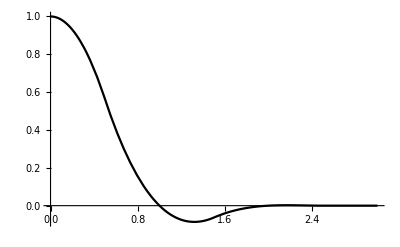

```mathematica
Plot[h[x]/.GenSols[[1]],{x,0,3},PlotStyle->Black,Background->White]
```

```mathematica
RegionXY[k_]:={Quotient[k,2],1+Quotient[-k,2]};
Regions=Table[RegionXY[k],{k,-4,7}]-1/2
```

{{-5/2,5/2},{-5/2,3/2},{-3/2,3/2},{-3/2,1/2},{-1/2,1/2},{-1/2,-1/2},{1/2,-1/2},{1/2,-3/2},{3/2,-3/2},{3/2,-5/2},{5/2,-5/2},{5/2,-7/2}}

```mathematica
GenSol=GenSols[[1]];
f[x_,y_]:=f[x]f[y];
φ=1/2;
W[k_]:=Piecewise[{{0, k<0}, {φ^2/2, k==0}, {1-(1-φ)^2/2, k==1}, {1, True}}];
SumF=∑_(i=-5)^6 ∑_(j=-5)^6 W[i-j]f[x-i,y-j]/.GenSol;
SimplifySquare[f_,x0_,y0_]:=Simplify[f,x>x0&&x<x0+1&&y>y0&&y<y0+1];
DSimplifySquare[f_,{x0_,y0_}]:=Simplify[D[SimplifySquare[f,x0,y0],{{x,y}}]];
DSumF=ParallelMap[DSimplifySquare[SumF,#]&,Regions];
```

```mathematica
AnisoInt[df_,{x0_,y0_}]:=Simplify[Integrate[Expand[(df.{1,1})^2],{x,x0,x0+1},{y,y0,y0+1}]];
AnisoInts=Parallelize[MapThread[AnisoInt,{DSumF,Regions}]];
Err=Simplify[Total[AnisoInts]]
```

94211027/660602880